# Project 8: Steepest Ascent

## (1)

```mathematica
Clear[f,df,argMax,x,y,X,h,threshold,A,B,G]
```

```mathematica
f[x_,y_] := (Cos[x]*Cos[y])/(6+x^2+y^2);
df[x_,y_]=Grad[f[x,y],{x,y}];
```

## (2)

```mathematica
f[1.0,2.0]

df[1.0,2.0]
```

-0.0204405

{0.0355506,-0.0372303}

```mathematica
g = {1.0,2.0};
f[g]
df[g]
```

f[{1.,2.}]

df[{1.,2.}]

```mathematica
Apply[f,g]
Apply[df,g]
```

-0.0204405

{0.0355506,-0.0372303}

## (3)

```mathematica
Plot3D[f[x,y],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

## (4)

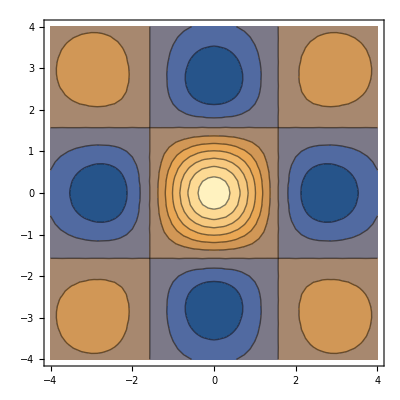

```mathematica
A = ContourPlot[f[x,y],{x,-4,4},{y,-4,4}]
```

## (5)

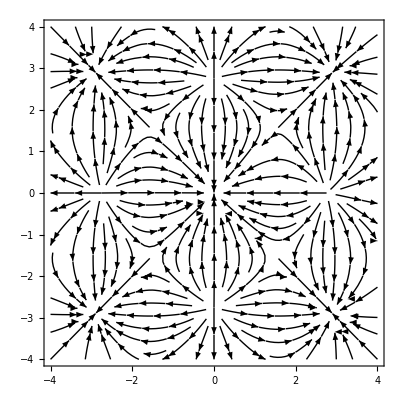

```mathematica
B = StreamPlot[df[x,y],{x,-4,4},{y,-4,4}, StreamStyle-> Black]
```

## (6)

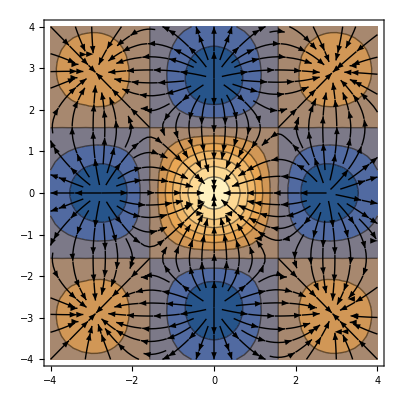

```mathematica
Show[A, B]
```

## (7)

```mathematica
argMax[f_,df_,z_]:= Module[{d,x,X,h,threshold},
x= z;
X={x};
h=0.01;
threshold = 0.001;
While[Sqrt[df[x].df[x]]> threshold,
x= x+h*df[x];
X= Append[X,x]];
Print[x];
Print[df[x]]]
```

## (8)

```mathematica
Clear[F,dF,x,X];
```

```mathematica
F[x_]:=(Cos[x[[1]]] *Cos[x[[2]]])/(6+(x[[1]])^2+(x[[2]])^2);
dF[x_]:= {-(2 (x[[1]]) Cos[x[[1]]] Cos[x[[2]]])/((6+(x[[1]])^2+(x[[2]])^2)^2)-(Cos[x[[2]]] Sin[x[[1]]])/(6+(x[[1]])^2+(x[[2]])^2),-(2(x[[2]]) Cos[x[[1]]] Cos[x[[2]]])/((6+(x[[1]])^2+(x[[2]])^2)^2)-(Cos[x[[1]]] Sin[x[[2]]])/(6+(x[[1]])^2+(x[[2]])^2)};
```

```mathematica
argMax[F,dF,{0.20,2.65}]
argMax[F,dF,{0.20,2.6}]
```

{2.87553,2.87598}

{0.000717793,0.000696203}

{0.00268314,0.00360691}

{-0.000596247,-0.000801528}

{0.2,2.65}

{2.87554,2.87598}

{0.000717267,0.00069592}

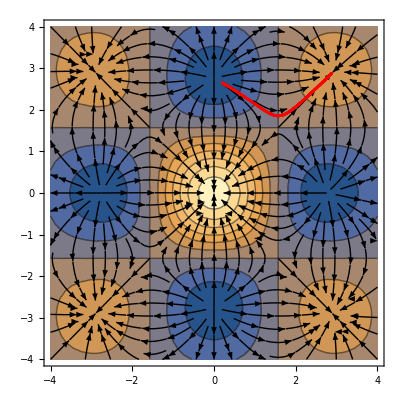

```mathematica
x={0.2,2.65}
X={x};
threshold=0.001;
h=0.1;
While[Sqrt[dF[x].dF[x]]> threshold,
x= x+h*dF[x];
X= Append[X,x]]
Print[x]
Print[dF[x]]
G = ListPlot[X, PlotRange -> {{-4,4},{-4,4}}, PlotStyle -> Red];
Show [A,B,G]
```

{0.2,2.6}

{0.00265192,0.00354029}

{-0.000589309,-0.000786723}

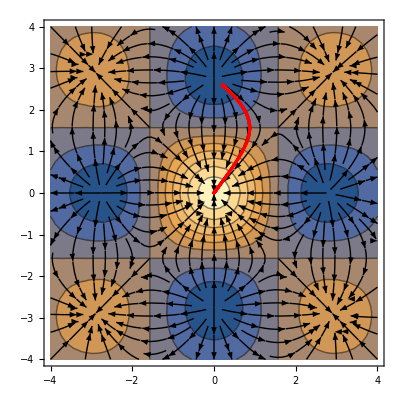

```mathematica
x={0.2,2.60}
X={x};
threshold=0.001;
h=0.1;
While[Sqrt[dF[x].dF[x]]> threshold,
x= x+h*dF[x];
X= Append[X,x]]
Print[x]
Print[dF[x]]
G = ListPlot[X, PlotRange -> {{-4,4},{-4,4}}, PlotStyle -> Red];
Show [A,B,G]
```

As seen by the overlay of the three plots, the direction of the points in the ListPlot moves in different directions. By looking at the StreamPlot to see the gradient of the vector field, depending on where the original point is, the function will behave differently. The gradient of the point {0.2, 2.65} is {0.000717267,0.00069592} and the gradient of the point {0.2,2.6} is {-0.000589309,-0.000786723}, which shows different changes in direction of the two points in the x and y coordinate. Since the vector fields are not the same, this can significantly change the terminal point and yield very different results for each point.